## Annihilations

```mathematica
ClearSystemCache[]
Clear["Global`*"]
SetDirectory[NotebookDirectory[]];
```

```mathematica
TEMP = ((1*^3*1*^-9)/(1.16*^4)); (* GeV *)
NM     = (0.939); (* GeV *)
SOL   = 299792458.; (* ms^-1 *)
VELDISP  = 270.*^3;(* ms^-1 *)
NSVEL =  200.*^3 ;(* ms^-1 *)
G       =  6.67408*^-11; (*Grav Constant*)
TT = ((1*^10 * 3.154*^7)/(6.58*^-16)*1*^9); (* therm time *)
```

## Matrix Elements

```mathematica
(*================================================================================================================================================================*)

(* s = scalar, p = psedoscalar, v = vector, a = axialvector *)

ssME[q_, dmm_] := 16*NM^2*dmm^2;

psME[q_, dmm_] := 4*NM^2*q^2;

pspsME[q_, dmm_] := q^4;
```

## Coupling constants (neutrons)

```mathematica
responseFn[q_, q0_] := (NM^2*q0)/(Pi*q);
denomInt[ki_, ME_, dmm_] :=Module[
{q, q0, cos},
q = √(ki^2+kp^2- 2* ki*kp*cos);
q0 = 1/(2*dmm)*(ki^2- kp^2);
 Integrate[(ME[q, dmm]*q0)/(16*NM^2*dmm^2*(2*π)^2)*kp^2*responseFn[q, q0],{kp, 0, ki}, {cos, -1, 1}, Assumptions->{ki>kp, kp>0}]
];

gSqr[ME_, dmm_, temp_] := Module[(*coupling constant squared in Natural units*)
{k0, kn},
k0 = dmm/3;
kn = √(4*dmm*temp);
-1/TT*Integrate[ki/(dmm*denomInt[ki, ME, dmm]), {ki, k0, kn}, Assumptions->{k0>kn, kn>0}]
];
```

## Interpolating Functions

#### Load in data

```mathematica
EoSHeaders = Import["eos_24_lowmass.dat"];
Dataset[EoSHeaders[[1,All]]] (*Print out headings so I know what I'm doing *)
EoSData =Drop[EoSHeaders, 1] ;(* Remove Headings *)
```

Dataset[<>]

Make Interpolating Functions

```mathematica
radius = EoSData[[All,1]];

rMin = radius[[1]];
rMax = 12.1;

muFn     = Interpolation[ EoSData[[All, {1,8}]] ]; (* Chemical potential in MeV *)

nb          = EoSData[[All,3]];
Yn          = EoSData[[All, 7]];
muList = EoSData[[All, 8]];

ndList = nb*Yn;
nd          = Interpolation[ Transpose[{radius,nb*Yn}]]; (* Neutron density in fm^-1*)

NSMass=   Interpolation[EoSData[[All, {1, 2}]]]; (* In units of M_⊙ *) 
(*================================================================================================================================================================*)
potentialInside[rad_?NumericQ] := NIntegrate[(NSMass[r])/r^2, {r, rMin, rad}]*(G*2.*^30)/(1.*^3*SOL^2);
pot = Interpolation[Table[potentialInside[x], {x, rMin, rMax}]];
potentialOutside[rad_] := (2.*G*NSMass[rMax]*2.*^30)/(rad*1.*^3*SOL^2);
(*================================================================================================================================================================*)
```

```mathematica
NIntegrate[Exp[(-pot[x])/(1.*^-9)], {x, rMin, 11.}]
```

0.000813462

## Masses and other things

```mathematica
lepMasses = {0.5109989461, 105.6583745, 1776.86, 0,0,0}*1.*^-3;(* {e, μ, τ,Subscript[ν, e], Subscript[ν, μ], Subscript[ν, τ]}*)
quarkMasses = {2.2*^-3, 4.7*^-3, 95*^-3, 1.257, 4.18, 173};(* {u, d, s, c, b, t}  *) 

vAvg[mx_, temp_] := (6*temp)/mx;

capRate = 1.*^22; (*test cap rate*)
```

## Number density

```mathematica
ndFac[mx_?NumericQ, temp_?NumericQ] := Module[
{Subscript[r, th]},
Subscript[r, th] = 
NIntegrate[Exp[(-2.*mx*pot[rad])/temp], {rad, rMin, rMax}]/(4.*Pi*(NIntegrate[Exp[(-mx*pot[rad])/temp], {rad, rMin, rMax}])^2)
];
```

```mathematica
ndFac[1., 1*^-9]
```

69.7456

## Thermally averaged annihilation cross sections

```mathematica
ssACS[mx_, temp_] :=gSqr[ssME, mx, temp]*(Sum[mx^2/(16.*π)*(1. - mf^2/mx^2)^(3/2)*vAvg[mx, temp], {mf, Select[lepMasses, #≤ mx&]}]+Sum[(3.*mx^2)/(16.*π)*(1. - mf^2/mx^2)^(3/2)*vAvg[mx, temp], {mf, Select[quarkMasses, #≤ mx&]}] );
(*================================================================================================================================================================*)

ppACS[mx_, temp_] :=gSqr[pspsME, mx, temp]* (Sum[1./(4.*π)*mx^2 Sqrt[1. - mf^2/mx^2]*(1. + ((2.*mx^2- mf)/(8.*(mx^2 - mf^2)))*vAvg[mx, temp]),{mf, Select[lepMasses, #≤ mx&]}] +  Sum[3./(4.*π)*mx^2 Sqrt[1. - mf^2/mx^2]*(1. +( (2.*mx^2- mf)/(8.*(mx^2 - mf^2)))*vAvg[mx, temp]),{mf, Select[quarkMasses, #≤ mx&]}]);

(*================================================================================================================================================================*)
```

## Equilibrium time

```mathematica
tEq[ACS_, mx_, temp_] := 1./Sqrt[capRate*ACS[mx,temp]];
```

```mathematica
tEq[ssACS, 1.*^6, 1.*^-5]
```

1.70297×10^6

```mathematica
EngineeringForm[1.868330410711743*^-12]
```

1.86833×10^-12

```mathematica
tab1 = With[{x:=10^xp},Table[{x,tEq[ssACS, x, 1.*^-10]},{xp, -6, 4, 0.25}]];
```

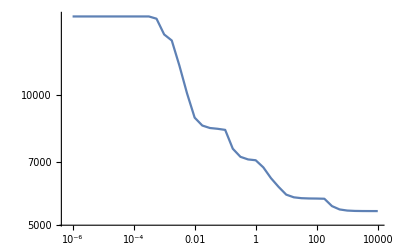

InterpolatingFunction::dmval: Input value {0.00389027} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0019449} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.000970384} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{x→-0.000267638}

```mathematica
ListLogLogPlot[tab1, Joined->True]
```

```mathematica
tab2 = Table[{10^t,y/.FindRoot[pot[y] == 3./2.*10^t, {y, rMax/2.}]}, {t, -10, -3}]
```

{{1/10000000000,1.00033},{1/1000000000,1.00109},{1/100000000,1.00347},{1/10000000,1.01101},{1/1000000,1.03485},{1/100000,1.11026},{1/10000,1.34909},{1/1000,2.10776}}

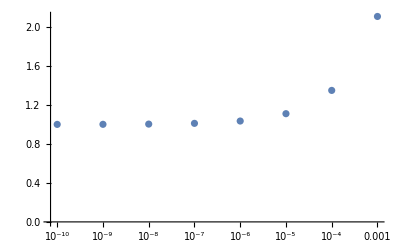

```mathematica
ListPlot[tab2, ScalingFunctions->{"Log", None}]
```